# Sex-specific epistasis and sexual antagonism - autosomal

```mathematica
Clear["Global`*"]
```

## Haplotypes and fitness

```mathematica
haplotypes={{Af,Bf},{Af,Bm},{Am,Bf},{Am,Bm},{Y}};
```

```mathematica
wlistM={
{{Am,Bm,Y},1},
{{Af,Bm,Y},1-sAm},
{{Am,Bf,Y},1-sBm},
{{Af,Bf,Y},(1-sBm)*(1-sAm)+4em}};
```

```mathematica
wlistF={
{{Am,Am,Bm,Bm},(1-sAf)(1-sBf)+4ef},
{{Af,Am,Bm,Bm},(1-hAf sAf)(1-sBf)+2 ef},
{{Af,Af,Bm,Bm},1-sBf},
{{Am,Am,Bf,Bm},(1-sAf)(1-hBf sBf)+2ef},
{{Af,Am,Bf,Bm},(1-hAf sAf)(1-hBf sBf)+ef},
{{Af,Af,Bf,Bm},1-hBf sBf},
{{Am,Am,Bf,Bf},1-sAf},
{{Af,Am,Bf,Bf},1-hAf sAf},
{{Af,Af,Bf,Bf},1}};
```

```mathematica
findW[genotype_]:=Module[{wlist,w,iter},
wlist=If[Count[genotype,Y]>0,wlistM,wlistF];
w=Null;
For[iter=1,iter≤Length[wlist],iter++,
If[wlist[[iter]][[1]]==Sort[genotype],w=wlist[[iter]][[2]]]
];
Return[w]
]
```

```mathematica
Table[{Join[haplotypes[[i]],haplotypes[[j]]],findW[Join[haplotypes[[i]],haplotypes[[j]]]]},{i,1,Length[haplotypes]-1},{j,1,Length[haplotypes]}]//MatrixForm
```

(({Af,Bf,Af,Bf}
1) | ({Af,Bf,Af,Bm}
1-hBf sBf) | ({Af,Bf,Am,Bf}
1-hAf sAf) | ({Af,Bf,Am,Bm}
ef+(1-hAf sAf) (1-hBf sBf)) | ({Af,Bf,Y}
4 em+(1-sAm) (1-sBm))
({Af,Bm,Af,Bf}
1-hBf sBf) | ({Af,Bm,Af,Bm}
1-sBf) | ({Af,Bm,Am,Bf}
ef+(1-hAf sAf) (1-hBf sBf)) | ({Af,Bm,Am,Bm}
2 ef+(1-hAf sAf) (1-sBf)) | ({Af,Bm,Y}
1-sAm)
({Am,Bf,Af,Bf}
1-hAf sAf) | ({Am,Bf,Af,Bm}
ef+(1-hAf sAf) (1-hBf sBf)) | ({Am,Bf,Am,Bf}
1-sAf) | ({Am,Bf,Am,Bm}
2 ef+(1-sAf) (1-hBf sBf)) | ({Am,Bf,Y}
1-sBm)
({Am,Bm,Af,Bf}
ef+(1-hAf sAf) (1-hBf sBf)) | ({Am,Bm,Af,Bm}
2 ef+(1-hAf sAf) (1-sBf)) | ({Am,Bm,Am,Bf}
2 ef+(1-sAf) (1-hBf sBf)) | ({Am,Bm,Am,Bm}
4 ef+(1-sAf) (1-sBf)) | ({Am,Bm,Y}
1))

```mathematica
w[haploNumMom_,haploNumDad_]:=Module[{genotype,wval},(*count the total numbers of female benefit and male benefit alleles *)
genotype=Join[haplotypes[[haploNumMom]],haplotypes[[haploNumDad]]];
Return[findW[genotype]]
]
```

Cross Table function

```mathematica
autosomeCross[haploNumMom_,haploNumDad_,haploNumGoal_]:=Module[{genotype,haploMom,haploDad,haploGoal,haploNoRec,haploRec},
haploMom=haplotypes[[haploNumMom]];
haploDad=haplotypes[[haploNumDad]];
haploGoal=haplotypes[[haploNumGoal]];
haploNoRec={haploMom,haploDad};
If[haploDad=={Y},Return[Count[haploNoRec,haploGoal]/2]];
haploRec={{haploMom[[1]],haploDad[[2]]},{haploDad[[1]],haploMom[[2]]}};
Return[Simplify[Count[haploNoRec,haploGoal]/2 (1-r)+Count[haploRec,haploGoal]/2 r]]
]
```

```mathematica
Table[autosomeCross[xi,xj,xk],{xi,1,4},{xj,1,5},{xk,1,5}]//MatrixForm
```

((1
0
0
0
0) | (1/2
1/2
0
0
0) | (1/2
0
1/2
0
0) | ((1-r)/2
r/2
r/2
(1-r)/2
0) | (1/2
0
0
0
1/2)
(1/2
1/2
0
0
0) | (0
1
0
0
0) | (r/2
(1-r)/2
(1-r)/2
r/2
0) | (0
1/2
0
1/2
0) | (0
1/2
0
0
1/2)
(1/2
0
1/2
0
0) | (r/2
(1-r)/2
(1-r)/2
r/2
0) | (0
0
1
0
0) | (0
0
1/2
1/2
0) | (0
0
1/2
0
1/2)
((1-r)/2
r/2
r/2
(1-r)/2
0) | (0
1/2
0
1/2
0) | (0
0
1/2
1/2
0) | (0
0
0
1
0) | (0
0
0
1/2
1/2))

## Recursions

```mathematica
ytplus1=Table[Sum[x[haploMom]y[haploDad]w[haploMom,haploDad]autosomeCross[haploMom,haploDad,haploGoal],{haploMom,1,Length[haplotypes]-1},{haploDad,{5}}],{haploGoal,1,Length[haplotypes]}]//Simplify;
xtplus1=Table[Sum[x[haploMom]y[haploDad]w[haploMom,haploDad]autosomeCross[haploMom,haploDad,haploGoal],{haploMom,1,Length[haplotypes]-1},{haploDad,1,Length[haplotypes]-1}],{haploGoal,1,Length[haplotypes]-1}]//Simplify;
```

```mathematica
ytplus1
```

{1/2 (4 em+(-1+sAm) (-1+sBm)) x[1] y[5],-1/2 (-1+sAm) x[2] y[5],-1/2 (-1+sBm) x[3] y[5],1/2 x[4] y[5],1/2 ((4 em+(-1+sAm) (-1+sBm)) x[1]+x[2]-sAm x[2]+x[3]-sBm x[3]+x[4]) y[5]}

```mathematica
wbarM=Total[ytplus1]//Simplify;
wbarF=Total[xtplus1]//Simplify;
```

```mathematica
Length[xtplus1]
```

4

```mathematica
haplotypes
```

{{Af,Bf},{Af,Bm},{Am,Bf},{Am,Bm},{Y}}

## Numerical iterations

```mathematica
iterate[{sAfs_,sAms_,sBfs_,sBms_},{hAfs_,hAms_,hBfs_,hBms_},{efs_,ems_},{rs_},{tend_}]:=Module[{data,xk,yk,subs,ti},
data=ConstantArray[ConstantArray[0,tend],9];
data[[All,1]]=Join[ConstantArray[0.25,4],ConstantArray[0.2,5]];
xk=xtplus1/wbarF/.{sAf->sAfs,sAm->sAms,sBf->sBfs,sBm->sBms,hAf->hAfs,hAm->hAms,hBf->hBfs,hBm->hBms,r->rs,ef->efs,em->ems};
yk=ytplus1/wbarM/.{sAf->sAfs,sAm->sAms,sBf->sBfs,sBm->sBms,hAf->hAfs,hAm->hAms,hBf->hBfs,hBm->hBms,r->rs,ef->efs,em->ems};
For[ti=2,ti≤tend,ti++,
subs=Flatten[Table[{x[xj]->data[[xj,ti-1]],y[xj]->data[[xj+4,ti-1]]},{xj,1,4}]];
data[[All,ti]]=Join[xk,yk]/.subs;
];
Return[data]
]
```

```mathematica
out=iterate[{0.2,0.4,0.2,0.4},{0.5,0.5,0.5,0.5},{0,0},{0.05},{1000}];
```

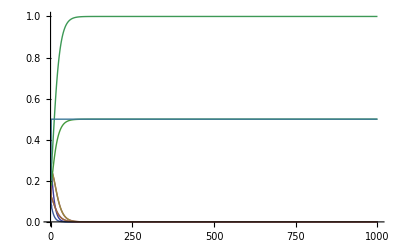

```mathematica
ListLinePlot[out,PlotRange->{0,1}]
```

```mathematica
out[[All,1000]]
```

{3.40515×10^-66,6.83041×10^-34,6.83041×10^-34,1.,7.13707×10^-67,2.21121×10^-34,2.21121×10^-34,0.5,1/2}

```mathematica
haplotypes
```

{{Af,Bf},{Af,Bm},{Am,Bf},{Am,Bm},{Y}}

## Export to C

Output directory

```mathematica
directory=$HomeDirectory<>"/Projects/sex_specific_epistasis/src/numerical/chromx/";
```

```mathematica
s2c[x_]:=ToString[CForm[x]]<>";\n\n";
```

```mathematica
str="wF = "<>s2c[wbarF];
str=str<>"wM = "<>s2c[wbarM];
For[iter=1,iter≤Length[haplotypes]-1,iter++,
str=str<>"x"<>ToString[iter]<>"tplus1 = "<>s2c[1/wF xtplus1[[iter]]];
];
For[iter=1,iter≤Length[haplotypes],iter++,
str=str<>"y"<>ToString[iter]<>"tplus1 = "<>s2c[1/wM ytplus1[[iter]]];
];
Export[directory<>"recursions.txt",str]
```

/home/bram/Projects/sex_specific_epistasis/src/numerical/chromx/recursions.txt